```mathematica
dir="/Users/simonfreedman/Code/cytoMod/shila/";
path="/txt_files/angle_correlations.txt";
```

ReadList::readn: Invalid real number found when reading from "/Users/simonfreedman/Code/cytoMod/shila/kl316.227766017_nm20/txt_files/angle_correlations.txt".

ReadList::readn: Invalid real number found when reading from "/Users/simonfreedman/Code/cytoMod/shila/kl316.227766017_nm30/txt_files/angle_correlations.txt".

ReadList::readn: Invalid real number found when reading from "/Users/simonfreedman/Code/cytoMod/shila/kl316.227766017_nm40/txt_files/angle_correlations.txt".

General::stop: Further output of ReadList :: readn will be suppressed during this calculation.

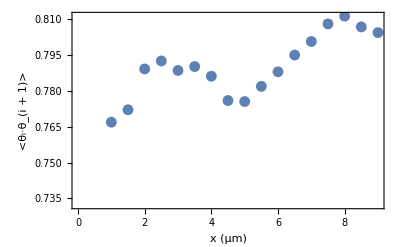
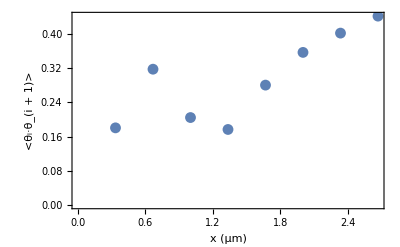
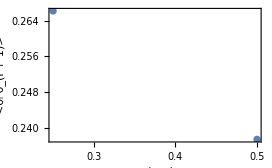
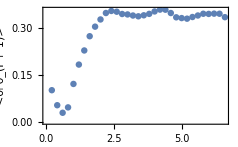
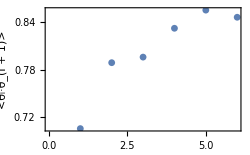
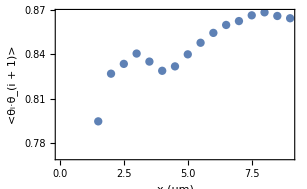
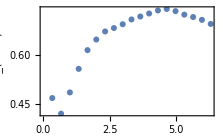
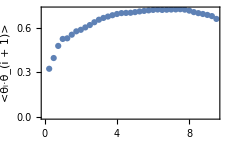
{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}}

```mathematica
Table[{d=ReadList[dir<>"kl"<>ToString[kl]<>"_nm"<>ToString[nm]<>path,Number, RecordLists->True];
ListPlot[d,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = "<>ToString[kl] <>"pN/μm;nmonomers ="<>ToString[nm]}]},{kl,{"1.0","3.16227766017","10.0","31.6227766017","100.0","316.227766017"}},{nm,{10,20,30,40,50}}]
```

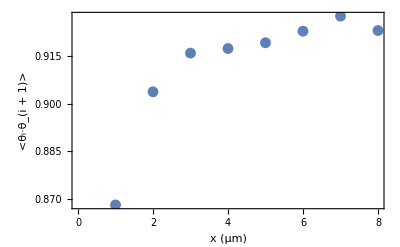

```mathematica
d3=ReadList[dir<>f3,Number, RecordLists->True];
ListPlot[d3,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 100 pN/μm; nmonomers = 10"}]
```

```mathematica
f4="kl1_nm100/txt_files/angle_correlations.txt";
f5="kl10_nm100/txt_files/angle_correlations.txt";
f6="kl100_nm100/txt_files/angle_correlations.txt";
```

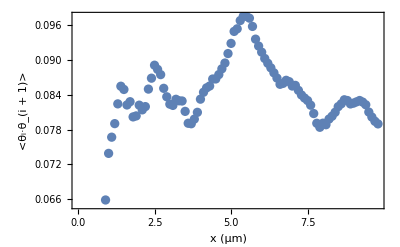

```mathematica
d4=ReadList[dir<>f4,Number, RecordLists->True];
ListPlot[d4,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 1 pN/μm; nmonomers = 100"}]
```

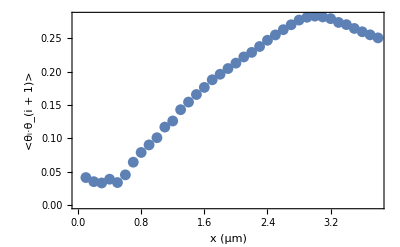

```mathematica
d5=ReadList[dir<>f5,Number, RecordLists->True];
ListPlot[d5,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 10 pN/μm; nmonomers = 100"}]
```

```mathematica
d6=ReadList[dir<>f6,Number, RecordLists->True];
ListPlot[d6,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 100 pN/μm; nmonomers = 100"}]
```

ReadList::readn: Invalid real number found when reading from "/Users/Simon/Code/cytoMod/shila/kl100_nm100/txt_files/angle_correlations.txt".

-Graphics-

ReadList::nffil: File not found during ReadList["/Users/simonfreedman/Code/cytoMod/shila/kl80_nm10/txt_files/angle_correlations.txt", Number, RecordLists → True].

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ReadList::nffil: File not found during ReadList["/Users/simonfreedman/Code/cytoMod/shila/kl80_nm20/txt_files/angle_correlations.txt", Number, RecordLists → True].

ReadList::nffil: File not found during ReadList["/Users/simonfreedman/Code/cytoMod/shila/kl80_nm30/txt_files/angle_correlations.txt", Number, RecordLists → True].

General::stop: Further output of ReadList :: nffil will be suppressed during this calculation.

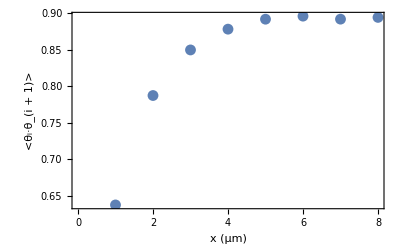
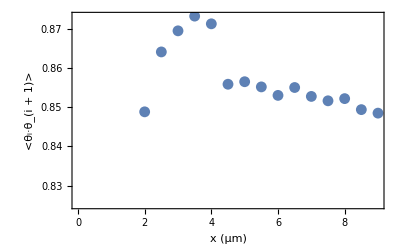
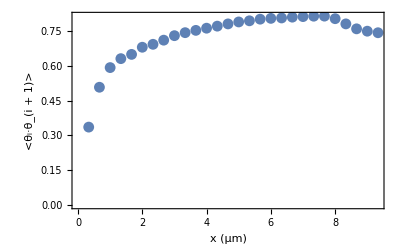
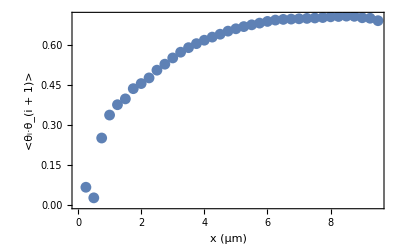
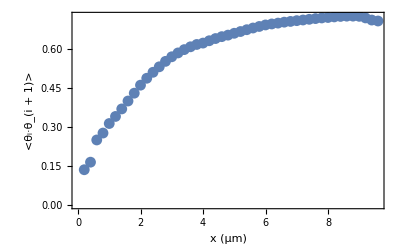
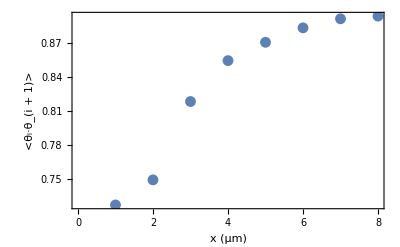
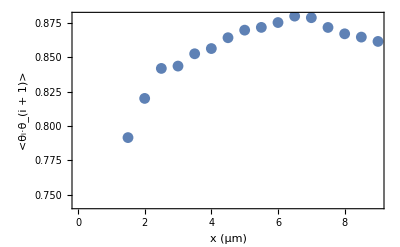
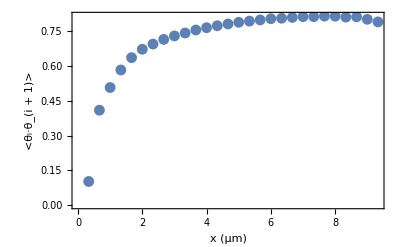
{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},{{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 80pN/μm;nmonomers =10}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 80pN/μm;nmonomers =20}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 80pN/μm;nmonomers =30}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 80pN/μm;nmonomers =40}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 80pN/μm;nmonomers =50}]}},{{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 90pN/μm;nmonomers =10}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 90pN/μm;nmonomers =20}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 90pN/μm;nmonomers =30}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 90pN/μm;nmonomers =40}]},{ListPlot[$Failed,Frame→True,FrameLabel→{x (μm),<θ_i·θ_(i + 1)>,link stiffness = 90pN/μm;nmonomers =50}]}}}

```mathematica
Table[{d=ReadList[dir<>"kl"<>ToString[kl]<>"_nm"<>ToString[nm]<>path,Number, RecordLists->True];
ListPlot[d,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = "<>ToString[kl] <>"pN/μm;nmonomers ="<>ToString[nm]}]},{kl,10,90,10},{nm,10,50,10}]
```

```mathematica
fmpath="/txt_files/fourier_modes.txt";
```

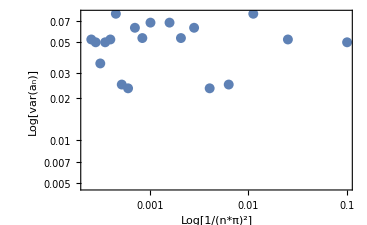
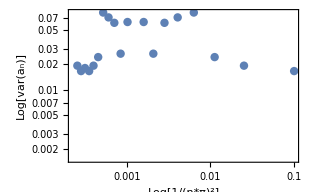
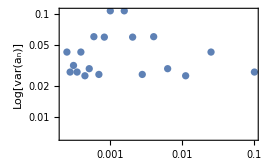

```mathematica
Table[{d=ReadList[dir<>"plf_kl"<>ToString[kl]<>"_nm"<>ToString[nm]<>fmpath,Number, RecordLists->True];
ListLogLogPlot[d,Frame->True, FrameLabel->{"Log[1/(n*π)^2] ","Log[var(a_n)]","link stiffness = "<>ToString[kl] <>"pN/μm;nmonomers ="<>ToString[nm]}]},{kl,10,30,10},{nm,10,10,10}]
```

## START HERE

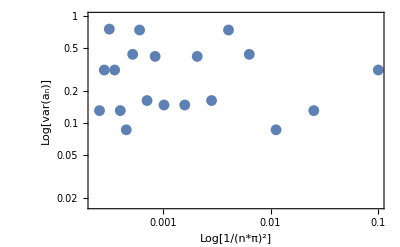
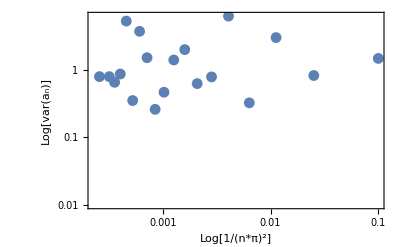
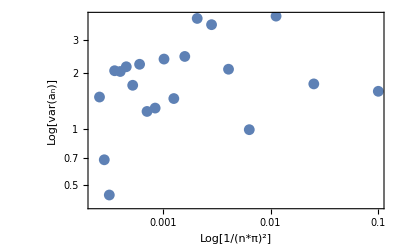
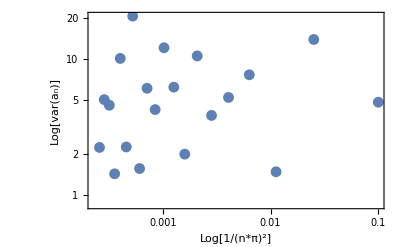
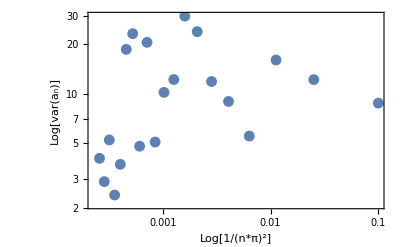
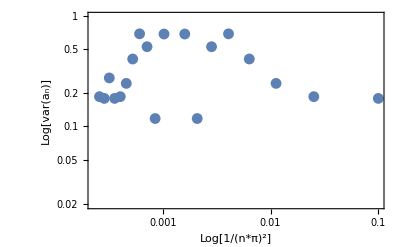
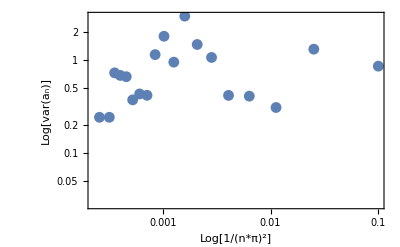
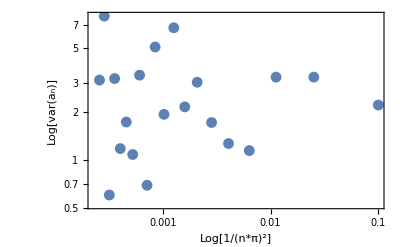

```mathematica
Table[{d=ReadList[dir<>"plf_kl"<>ToString[kl]<>"_nm"<>ToString[nm]<>fmpath,Number, RecordLists->True];
ListLogLogPlot[d,Frame->True, FrameLabel->{"Log[1/(n*π)^2] ","Log[var(a_n)]","link stiffness = "<>ToString[kl] <>"pN/μm;nmonomers ="<>ToString[nm]}]},{kl,10,50,10},{nm,10,50,10}]
```

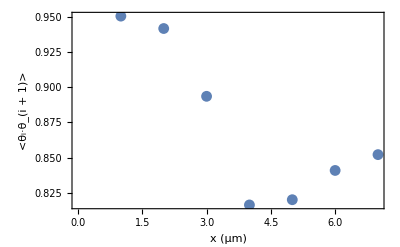
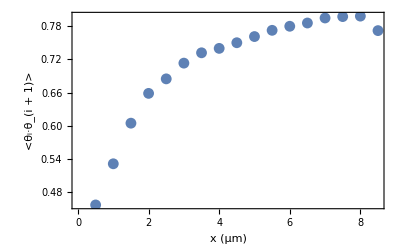
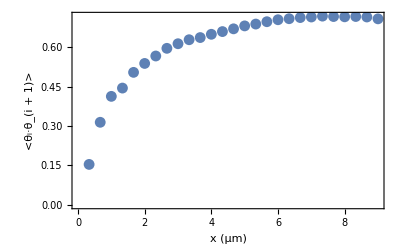
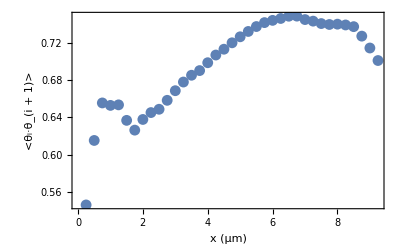
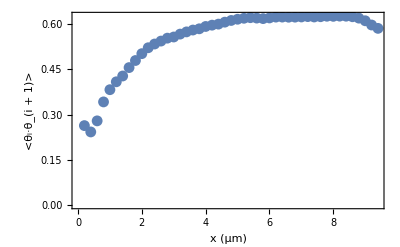
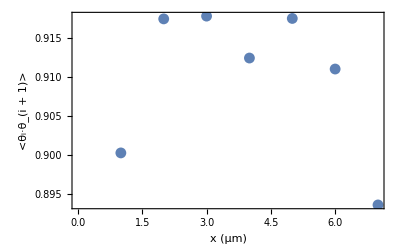
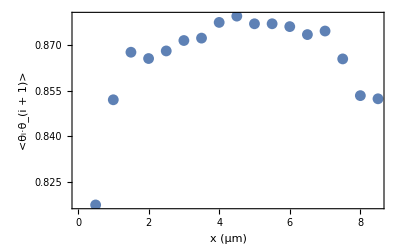
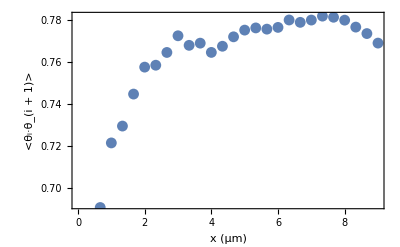

```mathematica
Table[{d=ReadList[dir<>"pl_kl"<>ToString[kl]<>"_nm"<>ToString[nm]<>path,Number, RecordLists->True];
ListPlot[d,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = "<>ToString[kl] <>"pN/μm;nmonomers ="<>ToString[nm]}]},{kl,10,50,10},{nm,10,50,10}]
```